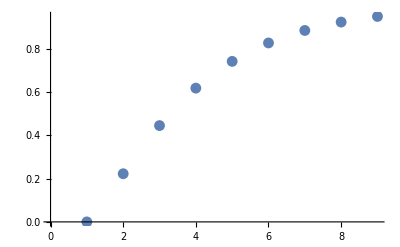

```mathematica
(*m个坑 n个球*)
P[m_,n_]=Sum[(-1)^(m-i)Binomial[m,i] i^n,{i,0,m}]/m^n;
ListPlot[
Table[P[3,n],
{n,2,10}]]
```

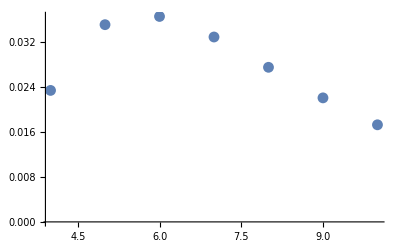

```mathematica
P0[m_,n_]=P[m-1,n-1]*((m-1)/m)^(n-1);
ListPlot[
Table[{n,P0[4,n]},
{n,4,10}]]
```

```mathematica
Sum[P0[4,n],{n,4,Infinity}]
```

1/4

```mathematica
25/12
```

3/128

Power::indet: Indeterminate expression 0^0 encountered.

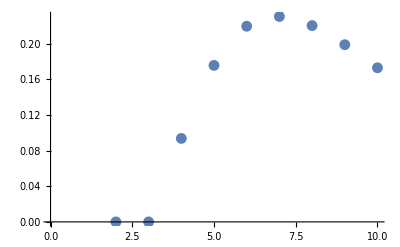

```mathematica
ListPlot[
Table[
P0[4,n]n,
{n,1,10}
]]
```